```mathematica
ClearAll["Global`*"]  (*two-stage third-order TSRK methods (TSRK23)*)
Remove["Global`*"]
ClearAll["p*"]
ClearAll["A*"]
ClearAll["v*"]
ClearAll["w*"]
ClearAll["b*"]
ClearAll["vv*"]
nn=3;
e=Table[1,{ii,nn},{i,1}];  e2=Table[1,{ii,nn-1},{i,1}];
v=({{w1*v1, v2, v3}});    

A=({{0, 0, 0}, {0, 0, 0}, {w1*a21, a22, 0}});  d=({{1, 0}, {0, 1}, {d31, 1-d31}});   L=({{-w1}, {0}});  b=({{b1, 1-b1}});
c=A.e+d.L; 
ce=c-e;

C1=DiagonalMatrix[c[[;;,1]]];Ce=DiagonalMatrix[ce[[;;,1]]];
τ2=-((c^2-d.(L^2))/2)+A.c;               τ3=-((c^3-d.(L^3))/6)+A.c^2/2;
τ4=-((c^4-d.(L^4))/4!)+A.c^3/3!;    τ5=-((c^5-d.(L^5))/5!)+A.c^4/4!;
τf2=τ2;   τf3=τ3-τ2;    τf4=τ4-τ3+τ2/2;  τf5=τ5-τ4+τ3/2-τ2/6;
(*τf2=0;   τf3=τ3;    τf4=τ4-τ3;  τf5=τ5-τ4+τ3/2;*)

p0=1-b.e2;  p1=1-b.L+Total[-v.e,2];    p2=(1-b.(L^2))/2+Total[-v.c,2];
p30=    (1-b.(L^3))/3+Total[-v.c^2 ,2];  pp31=Total[v.τ2,2];
(* d31=0; vv1=0; aa21=a21=0; *)(* w1=1;*)
 a21=0;
sol=Solve[p1==0&&p2==0&&p30==0&&pp31==0,{   v1,v2,d21,a22,b1}]  //FullSimplify
p0/.sol//FullSimplify   p1/.sol//FullSimplify      p2/.sol//FullSimplify 
p30/.sol//FullSimplify    pp31/.sol//FullSimplify
```

ClearAll::wrsym: Symbol AASTriangle is Protected.

ClearAll::wrsym: Symbol AbelianGroup is Protected.

ClearAll::wrsym: Symbol Abort is Protected.

General::stop: Further output of ClearAll::wrsym will be suppressed during this calculation.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{v1→(1+w1+(2 √d31 v3-3 d31 v3) w1^2)/w1^3,v2→(-1+4 √d31-3 d31) v3+(1+w1)^2/w1^2,a22→(-√d31+d31) w1,b1→(2+3 w1-6 (-√d31+d31) v3 w1^2)/w1^3},{v1→(1+w1-(2 √d31+3 d31) v3 w1^2)/w1^3,v2→-((1+4 √d31+3 d31) v3)+(1+w1)^2/w1^2,a22→(√d31+d31) w1,b1→(2+3 w1-6 (√d31+d31) v3 w1^2)/w1^3}}

{{{0}},{{0}}}[{{{0}},{{0}}}[{{{0}},{{0}}}]]

{0,0}[{{{0}},{{0}}}]

```mathematica
ClearAll["Global`*"]  (*EX TSRK23  A-stable*)
Remove["Global`*"]
ClearAll["x*"]
ClearAll["y*"]
ClearAll["f*"]
ClearAll["z*"]
(*ad=(√3)/3;bk=8/10; *)
 w1=1;
a21=0;   

v1=(1+w1-(2 √d31+3 d31) v3 w1^2)/w1^3;        v2=-((1+4 √d31+3 d31) v3)+(1+w1)^2/w1^2;
a22=(√d31+d31) w1;                            b1=(2+3 w1-6 (√d31+d31) v3 w1^2)/w1^3;

 b2=1-b1;
 d32=1-d31;

ff=b1/k+b2+  (v1*z)/k +v2*z  +((d31/k+d32)/(1-a22*z))v3*z
sol=Solve[ff==k,{ k}]//FullSimplify
```

-4+6 (√d31+d31) v3+(5-6 (√d31+d31) v3)/k+((2-(2 √d31+3 d31) v3) z)/k+(4-(1+4 √d31+3 d31) v3) z+((1-d31+d31/k) v3 z)/(1-(√d31+d31) z)

{{k→1/(2 (-1+√d31 z+d31 z))(4-6 √d31 v3-6 d31 v3+2 (-2+(√d31+d31) (-2+(2+3 (√d31+d31)) v3)) z-(√d31+d31) (-4+v3+4 √d31 v3+3 d31 v3) z^2+√(-4 (-1+√d31 z+d31 z) (5+2 z+(1+√d31) √d31 (-z (5+2 z)+v3 (-6+z (-2+3 d31 (2+z)+2 √d31 (3+z)))))+(4 (-1+z)+(√d31+d31) (-4 (-1+z) z+v3 (6+z (-4+3 d31 (-2+z)+z+√d31 (-6+4 z)))))^2))},{k→-1/(2 (-1+√d31 z+d31 z))(-4+6 √d31 v3+6 d31 v3+4 z-2 (√d31+d31) (-2+(2+3 (√d31+d31)) v3) z+(√d31+d31) (-4+v3+4 √d31 v3+3 d31 v3) z^2+√(-4 (-1+√d31 z+d31 z) (5+2 z+(1+√d31) √d31 (-z (5+2 z)+v3 (-6+z (-2+3 d31 (2+z)+2 √d31 (3+z)))))+(4 (-1+z)+(√d31+d31) (-4 (-1+z) z+v3 (6+z (-4+3 d31 (-2+z)+z+√d31 (-6+4 z)))))^2))}}

0.793291

2.35442

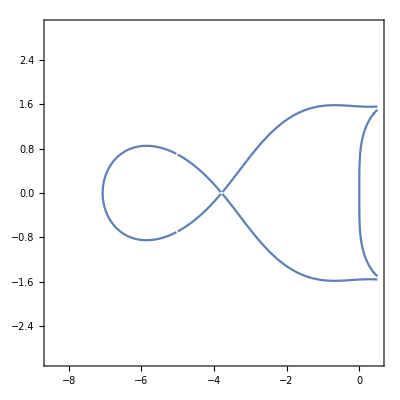

```mathematica
ClearAll["Global`*"]  (*EX TSRK23 A-stable*)
Remove["Global`*"]
ClearAll["x*"]
ClearAll["y*"]
ClearAll["f*"]
ClearAll["z*"]
v3=2.0;d31=((2-√2)/2)^2;

z=x+I*y;

f1[z_]:=1/(2 (-1+√d31 z+d31 z))(4-6 √d31 v3-6 d31 v3+2 (-2+(√d31+d31) (-2+(2+3 (√d31+d31)) v3)) z-(√d31+d31) (-4+v3+4 √d31 v3+3 d31 v3) z^2+√(-4 (-1+√d31 z+d31 z) (5+2 z+(1+√d31) √d31 (-z (5+2 z)+v3 (-6+z (-2+3 d31 (2+z)+2 √d31 (3+z)))))+(4 (-1+z)+(√d31+d31) (-4 (-1+z) z+v3 (6+z (-4+3 d31 (-2+z)+z+√d31 (-6+4 z)))))^2));
f2[z_]:=-1/(2 (-1+√d31 z+d31 z))(-4+6 √d31 v3+6 d31 v3+4 z-2 (√d31+d31) (-2+(2+3 (√d31+d31)) v3) z+(√d31+d31) (-4+v3+4 √d31 v3+3 d31 v3) z^2+√(-4 (-1+√d31 z+d31 z) (5+2 z+(1+√d31) √d31 (-z (5+2 z)+v3 (-6+z (-2+3 d31 (2+z)+2 √d31 (3+z)))))+(4 (-1+z)+(√d31+d31) (-4 (-1+z) z+v3 (6+z (-4+3 d31 (-2+z)+z+√d31 (-6+4 z)))))^2));
 
x=-6; y=2.;
Abs[f1[z]]//N    
 Abs[f2[z]]//N

ss1=ContourPlot[N[Abs[f1[z]]]==1.0,{x,-8.5,0.5},{y,-3,3},AspectRatio->1.2,PlotPoints->100] ;
ss2=ContourPlot[N[Abs[f2[z]]]==1.0,{x,-8.5,0.5},{y,-3,3},AspectRatio->1.2,PlotPoints->100] ;
Show[ss1,ss2,AspectRatio->1.0]
```

4.63864

0.0418467

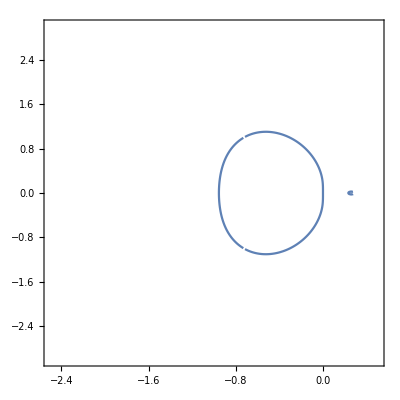

```mathematica
ClearAll["Global`*"]  (*EX TSRK23 A-stable*)
Remove["Global`*"]
ClearAll["x*"]
ClearAll["y*"]
ClearAll["f*"]
ClearAll["z*"]
v3=0.2;d31=1.5^2;

z=x+I*y;

f1[z_]:=1/(2 (-1+√d31 z+d31 z))(4-6 √d31 v3-6 d31 v3+2 (-2+(√d31+d31) (-2+(2+3 (√d31+d31)) v3)) z-(√d31+d31) (-4+v3+4 √d31 v3+3 d31 v3) z^2+√(-4 (-1+√d31 z+d31 z) (5+2 z+(1+√d31) √d31 (-z (5+2 z)+v3 (-6+z (-2+3 d31 (2+z)+2 √d31 (3+z)))))+(4 (-1+z)+(√d31+d31) (-4 (-1+z) z+v3 (6+z (-4+3 d31 (-2+z)+z+√d31 (-6+4 z)))))^2));
f2[z_]:=-1/(2 (-1+√d31 z+d31 z))(-4+6 √d31 v3+6 d31 v3+4 z-2 (√d31+d31) (-2+(2+3 (√d31+d31)) v3) z+(√d31+d31) (-4+v3+4 √d31 v3+3 d31 v3) z^2+√(-4 (-1+√d31 z+d31 z) (5+2 z+(1+√d31) √d31 (-z (5+2 z)+v3 (-6+z (-2+3 d31 (2+z)+2 √d31 (3+z)))))+(4 (-1+z)+(√d31+d31) (-4 (-1+z) z+v3 (6+z (-4+3 d31 (-2+z)+z+√d31 (-6+4 z)))))^2));
 
x=-4; y=1.;
Abs[f1[z]]//N    
 Abs[f2[z]]//N

ss1=ContourPlot[N[Abs[f1[z]]]==1.0,{x,-2.5,0.5},{y,-3,3},AspectRatio->1.2,PlotPoints->100] ;
ss2=ContourPlot[N[Abs[f2[z]]]==1.0,{x,-2.5,0.5},{y,-3,3},AspectRatio->1.2,PlotPoints->100] ;
Show[ss1,ss2,AspectRatio->1.0]
pp1=ss1[[1,1,1]]//MatrixForm
pp1=ss2[[1,1,1]]//MatrixForm
```